### TMM functions

```mathematica
ts1[nIncident_,nFinal_,θIncident_,θFinal_]:=(2nIncident Cos[θIncident])/(nIncident Cos[θIncident]+nFinal Cos[θFinal]);
tp1[nIncident_,nFinal_,θIncident_,θFinal_]:=(2nIncident Cos[θIncident])/(nFinal Cos[θIncident]+nIncident Cos[θFinal]);
rs1[nIncident_,nFinal_,θIncident_,θFinal_]:=(nIncident Cos[θIncident]-nFinal Cos[θFinal])/(nIncident Cos[θIncident]+nFinal Cos[θFinal]);
rp1[nIncident_,nFinal_,θIncident_,θFinal_]:=(nFinal Cos[θIncident]-nIncident Cos[θFinal])/(nFinal Cos[θIncident]+nIncident Cos[θFinal]);
```

.00.00.b4h.12.02.00.00.aa\[CapitalCCedilla]T.1f\[UGrave].7f.00.00.00.00\[CapitalADoubleDot]h.12.02.00.00.00.00.00.00.12.02.00.00.00.10.00.00.00.00.00.00.00.00.00.00\[UGrave].7f.00.00$.04\[CapitalADoubleDot]h.12.02.00.00.10.10.00.00.00.00.00.00.02.00.00.00.12.02.00.00.1c2\[CapitalUAcute]L\[Divide].7f.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00\[AGrave]\[AGrave]0H.12.02.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00	.00.00.00.00.00.00.00\[PlusMinus].01.01.00.00.00.00.00.00;C\[PlusMinus].1c\[UGrave].7f.00.00.06.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00\;.97\[CapitalOHat].7f.84.00.00\[IDoubleDot]n\[PlusMinus].1c\[UGrave].7f.00.00\[PlusMinus].01.01.00.00.00.00.00.00\[SZ]7\[CapitalUAcute]L

```mathematica
RepeatedDotProduct[ListOfMatrices_]:=Block[{n=Length[ListOfMatrices],index,SoFar},
If[n==0,Return[{{1,0},{0,1}}]];
SoFar=ListOfMatrices[[1]];
For[index=2,index≤n,index++,SoFar=SoFar . ListOfMatrices[[index]]];
Return[SoFar];];
```

```mathematica
FresnelCalc[nList_,dList_,θ0_,λvacuum_]:=
Block[{NumMedia,δ,θList,tsList,tpList,rsList,rpList,MsList,MpList,MsTemp,MpTemp,Ms,Mp,rstotal,rptotal,tstotal,tptotal,Rs,Rp,Ts,Tp,RUnpol,TUnpol,temp,ψ,Δ},
NumMedia=Length[nList];
If[(Length[dList]≠NumMedia) || (dList[[1]]≠∞)||(dList[[NumMedia]]≠∞),Return["Error in d or n!"]];
If[Im[nList[[1]]]≠0 || Im[θ0]≠ 0,Return["Sorry, program does not work correctly for a dissipative incoming medium."]]; 
(* θList is a list with, for each layer, the angle that the light travels through the layer. Computed with Snell's law. Note that the "angles" may be complex!*)
θList=ArcSin[(nList[[1]] Sin[θ0])/nList];
(* δ is a list with, for each layer (except the semi-infinite top and bottom "layers"),the phase accrued by traveling through that layer. δ[[i]] is what Sernelius would call Subscript[δ, i], apart from the renumbering.*)
δ=Table[If[i==1||i==NumMedia,Null,(2π dList[[i]])/λvacuum nList[[i]] Cos[θList[[i]]]],{i,1,NumMedia}];
(* tsList, tpList, rsList, rpList are the transmission and reflection amplitudes at each of the interfaces. For example,tsList[[i,j]] corresponds to what Sernelius would call Subscript[t, i,j] for s-polarization (apart from the renumbering),and is the (complex) ratio of Subscript[E, transmitted]/Subscript[E, original], where the "original" comes from the i side and the "transmitted" is on the j side. We're only interested in the case that j=i+1; the rest don't enter the calculation.*)
tsList=Table[If[j-i==1,ts1[nList[[i]],nList[[j]],θList[[i]],θList[[j]]],Null],{i,1,NumMedia-1},{j,1,NumMedia}];
tpList=Table[If[j-i==1,tp1[nList[[i]],nList[[j]],θList[[i]],θList[[j]]],Null],{i,1,NumMedia-1},{j,1,NumMedia}];
rsList=Table[If[j-i==1,rs1[nList[[i]],nList[[j]],θList[[i]],θList[[j]]],Null],{i,1,NumMedia-1},{j,1,NumMedia}];
rpList=Table[If[j-i==1,rp1[nList[[i]],nList[[j]],θList[[i]],θList[[j]]],Null],{i,1,NumMedia-1},{j,1,NumMedia}];
(* At the interface between the (n-1)st and nth material, let Subscript[x, n] be the amplitude of the wave on the (n-1)st side heading towards the boundary, and let Subscript[y, n] be the amplitude of the wave on the (n-1)st side heading away from the boundary. Then ({{Subscript[x, n]}, {Subscript[y, n]}})=Subscript[M, n]({{Subscript[x, n+1]}, {Subscript[y, n+1]}}), where Subscript[M, n]=1/Subscript[t, n-1,n]({{1, Subscript[r, n-1,n]}, {Subscript[r, n-1,n], 1}})({{Exp[-ⅈ Subscript[δ, n]], 0}, {0, Exp[ⅈ Subscript[δ, n]]}}),from Sernelius. Subscript[M, 1] and Subscript[M, NumMedia] are not defined. MsList[[n]] will be Subscript[M, n] for s-polarization, likewise MpList for p-polarization. Ms and Mp will be the matrix Sernelius calls "tilde-M", which you get by dot-producting all the Subscript[M, i], plus an extra factor at the end.*)
MsList=Table[If[i==1 || i== NumMedia,Null,1/tsList[[i-1,i]]({{1, rsList[[i-1,i]]}, {rsList[[i-1,i]], 1}}) . ({{Exp[-ⅈ δ[[i]]], 0}, {0, Exp[ⅈ δ[[i]]]}})],{i,1,NumMedia}];
MpList=Table[If[i==1 || i==NumMedia,Null,1/tpList[[i-1,i]]({{1, rpList[[i-1,i]]}, {rpList[[i-1,i]], 1}}) . ({{Exp[-ⅈ δ[[i]]], 0}, {0, Exp[ⅈ δ[[i]]]}})],{i,1,NumMedia}];
(* Ms and Mp will be the matrix Sernelius calls "tilde-M", which you get by dot-producting all the Subscript[M, i], plus an extra factor at the end.*)
MsTemp=RepeatedDotProduct[Take[MsList,{2,NumMedia-1}]];Ms = MsTemp . (1/tsList[[NumMedia-1,NumMedia]]({{1, rsList[[NumMedia-1,NumMedia]]}, {rsList[[NumMedia-1,NumMedia]], 1}}) );
MpTemp=RepeatedDotProduct[Take[MpList,{2,NumMedia-1}]];
Mp = MpTemp . (1/tpList[[NumMedia-1,NumMedia]]({{1, rpList[[NumMedia-1,NumMedia]]}, {rpList[[NumMedia-1,NumMedia]], 1}}) );
(*Net complex transmission and reflection amplitudes:*)
rstotal=Ms[[2,1]]/Ms[[1,1]];
rptotal=Mp[[2,1]]/Mp[[1,1]];
tstotal=1/Ms[[1,1]];
tptotal=1/Mp[[1,1]];
(*Net transmitted and reflected power,as a proportion of the incoming light power,for polarized and unpolarized incoming light. Don't forget,Ts,Tp,TUnpol represent the light power that enters the final, semi-infinite medium. If that medium has a complex index of refraction,the light will further attenuate as it travels through that medium to your detector,and you should take that into account separately.  See manual for discussion of formulas.*)
Rs=Abs[rstotal^2];
Rp=Abs[rptotal^2];
Ts=Abs[tstotal^2]×Re[nList[[NumMedia]]Cos[θList[[NumMedia]]]]/Re[nList[[1]]Cos[θList[[1]]]];
Tp=Abs[tptotal^2]×Re[nList[[NumMedia]]Conjugate[Cos[θList[[NumMedia]]]]]/Re[nList[[1]]Cos[θList[[1]]]];
RUnpol=1/2(Rs+Rp);
TUnpol=1/2(Ts+Tp);
ψ=ArcTan[Abs[rptotal/rstotal]];
Δ=Arg[-rptotal/rstotal];
Return[{Rs,Ts,Rp,Tp,RUnpol,TUnpol,ψ,Δ}];]
```

```mathematica
(* Next, ψ and Δ are the parameters measured in ellipsometry. Note that both are in RADIANS, not degrees. To get the value in degrees, divide by the degree symbol, e.g. " ψ/° ". (In Mathematica, the degree symbol is just treated as the number π/180 ~ 0.0175.) ψ is defined to be between 0 and +π/2, and Δ  between -π and +π.  Warning: There are different conventions for Δ in use, you may need to use "π-Δ" or "2π-Δ" or "Δ-π", etc., to get agreement with your ellipsometer output.  *)
```

```mathematica
Rs[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[1]];
Ts[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[2]];
Rp[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[3]];
Tp[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[4]];
RUnpol[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[5]];
TUnpol[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[6]];
ψ[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[7]];
Δ[nList_,dList_,θ0_,λvacuum_]:=FresnelCalc[nList,dList,θ0,λvacuum][[8]];
```

### Import material refractive index

```mathematica
SetDirectory["...\\Transfer_Matrix_Method\\Files\\Refractive_indices"]; (*Set proper directory*)
hBNdat=Import["hBN.txt","Table"];
MoSe2dat=Import["MoSe2.txt","Table"];
SiO2dat=Import["SiO2.txt","Table"];
Sidat=Import["Si.txt","Table"];
```

```mathematica
nhBN=Interpolation[hBNdat];
nMoSe2=Interpolation[Table[{MoSe2dat[[i,1]],MoSe2dat[[i,2]]+I MoSe2dat[[i,3]]},{i,1,Length[MoSe2dat]}]];
nSiO2=Interpolation[Table[{SiO2dat[[i,1]],SiO2dat[[i,2]]+I SiO2dat[[i,3]]},{i,1,Length[SiO2dat]}]];
nSi=Interpolation[Table[{Sidat[[i,1]],Sidat[[i,2]]+I Sidat[[i,3]]},{i,1,Length[Sidat]}]];
```

### Model exciton as Lorentz oscillator

```mathematica
SetDirectory[NotebookDirectory[]]
```

G:\Shared drives\2DM\12_Code_Repository\02_TMD\02_TMD_cavity\Transfer_Matrix_Method

```mathematica
h=0.658;(*ℏ in meV*ps *)
c=300000;(*c in nm/ps*)
Exc[γr_,ω0_,γnr_,ω_]:=Sqrt[nMoSe2[1239.8/ω]^2-(h*c/(0.7ω0))(γr/(ω-ω0+I*γnr/2))]
```

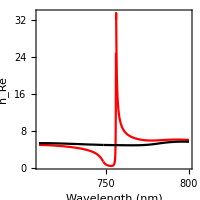

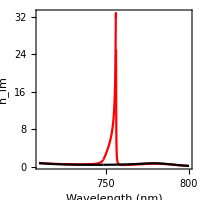

```mathematica
(*Black is bulk refractive index, Red shows excitonic response.*)

Plot[{Re[Exc[2.45,1239800/756.2,0.5,1239800/λ]],Re[nMoSe2[λ/1000]]},{λ,710,800},
PlotStyle->{Red,Black},
Frame->True,
FrameStyle->Directive[Thick,Black,11,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","n_Re"},
FrameTicksStyle->Directive[Black,Thick,10,FontFamily->"Cambria"],
AspectRatio->1,
PlotRange->{0,All},
ImageSize->200]

Plot[{Im[Exc[2.45,1239800/756.2,0.5,1239800/λ]],Im[nMoSe2[λ/1000]]},{λ,710,800},
PlotStyle->{Red,Black},
Frame->True,
FrameStyle->Directive[Thick,Black,11,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","n_Im"},
FrameTicksStyle->Directive[Black,Thick,10,FontFamily->"Cambria"],
AspectRatio->1,
PlotRange->{0,All},
ImageSize->200]
```

```mathematica
(*Export refractive index of ML TMD*)
(*exportTab = Join[Table[{λ,Re[Exc[2.15,1239800/756.2,1,1239.8/λ]],Im[Exc[2.15,1239800/756.2,1,1239.8/λ]]},{λ,.6,.8,0.001}]];
Export["FitMoSe2_Top.csv",exportTab,"FieldSeparators"->" "]*)
```

### Fit monolayer TMD

```mathematica
Clear[γr,ω0,γnr,λ0,ω, hbntop, hbnbottom]
(*refractive index of layers of device*)
nstruc[γr_,ω0_,γnr_,ω_]:={1.,nhBN[1239.8/ω],Exc[γr,ω0,γnr,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
(*dimensions of layers of device*)
dstruc[hbntop_,hbnbottom_]:={Infinity,hbntop,0.7,hbnbottom,285,Infinity};
```

```mathematica
(*Top Right ML Reflectivity*)
TR=Import["...\\Transfer_Matrix_Method\\Files\\TR_no-norm.dat","Table"]; (*Set proper directory*)
(*Bottom Right ML Reflectivity*)
BR=Import["...\\Transfer_Matrix_Method\\Files\\BR_no-norm.dat","Table"]; (*Set proper directory*)
```

```mathematica
Manipulate[ 
Show[
Plot[{Rp[nstruc[γr,1239800/λ0,γnr,1239800/λ],dstruc[hbntop, hbnbottom],0,λ]},{λ,600,800},
PlotRange->{{710,780},{0,0.6}},
PlotStyle->{{Red,Black}},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->400,
Frame->True,
FrameStyle->Directive[Thick,Black,11,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","Reflectance 0°"},
FrameTicksStyle->Directive[Black,Thick,10,FontFamily->"Cambria"],
AspectRatio->1,
PlotLegends->Placed[{"Fitting"},{Left,Bottom}],
PlotPoints->300],
ListPlot[{Table[{BR[[i,1]],A*BR[[i,2]]},{i,1,Length[TR]}]},
Joined->True,
PlotRange->All,
PlotLegends->Placed[{"Data"},{Left,Bottom}],
PlotStyle->{{Red},{Thin,Cyan}}]],
{{γr,2.15},0.1,3,0.05},
{{λ0,756.2},750,757,0.05},
{{γnr,1},0.05,3,0.05},
{{A,1.},0.5,1.5},
{{hbntop,58},50,70},
{{hbnbottom,59},50,70}]
```

```mathematica
(*This is the format to save the figure in svg:*)
Show[Plot[{Rp[nstruc[2.15,1239800/756.2,1,1239800/λ],dstruc[58, 59],0,λ]},{λ,600,800},PlotRange->{{710,780},{0,0.6}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{{720,740,760,780},None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,(*PlotLegends->Placed[{"Fitting"},{Left,Bottom}],*)PlotPoints->300],ListPlot[Table[{BR[[i,1]],BR[[i,2]]},{i,1,Length[TR]}],Joined->True,PlotRange->All,PlotStyle->{Thin,Red}]]
```

-Graphics-

### Cavity

```mathematica
SetDirectory[NotebookDirectory[]]
```

G:\Shared drives\2DM\12_Code_Repository\02_TMD\02_TMD_cavity\Transfer_Matrix_Method

```mathematica
(*Parameters: {γr,λ0,γnr,A,hbntop,hbnbottom}*)

pTR={2.45,756.2,0.5,1.1,63,63}; (*Top Right TMD is stacked on the bottom*)
pBR={2.15,756.2,1,1,58,59}; (*Bottom Right TMD is stacked on top*)
pZhou={4.38,758.2,0.2,1,70,68};(*parameters for Scuri et al.*)
```

### Different cavity configurations

Case 1: ML TMD

```mathematica
dcav={Infinity,130,0.7,20,285,Infinity};
ncav[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}

Plot[{Rp[ncav[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500]
```

-Graphics-

Case 2: TMD - Air - TMD

```mathematica
dcav={Infinity,0.7,350,0.7,Infinity};
ncav[ω_]:={1.,Exc[4.38,1239800/756.2,0.2,ω],1.,Exc[4.38,1239800/756.2,0.2,ω],1.}

Plot[{Rp[ncav[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500]
```

-Graphics-

Case 3: hBN - TMD - hBN - TMD - hBN

```mathematica
dcav={Infinity,35,0.7,100,0.7,35,Infinity};
ncav[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],1.}

Plot[{Rp[ncav[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500]
```

-Graphics-

Case 4: hBN - TMD - hBN - TMD - hBN - SiO_2 - Si

```mathematica
dcav={Infinity,60,0.7,120,0.7,60,285,Infinity};
ncav[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}

Plot[{Rp[ncav[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500]
```

-Graphics-

3 different ML mirrors in air

```mathematica
dcav={Infinity,0.7,Infinity};
ncavZ[ω_]:={1.,Exc[4.38,1239800/756.2,0.2,ω],1.}
ncavBot[ω_]:={1.,Exc[2.15,1239800/756.2,1,ω],1.}
ncavTop[ω_]:={1.,Exc[2.45,1239800/756.2,0.5,ω],1.}
```

```mathematica
Show[Plot[{Rp[ncavZ[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500],Plot[{Rp[ncavTop[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Blue},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500],
Plot[{Rp[ncavBot[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Red},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->500]]
```

-Graphics-

Same Γ_r, different Γ_nr

```mathematica
dcav={Infinity,60,0.7,60,285,Infinity};
ncav1[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.02,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
ncav2[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
ncav3[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,5,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}

Show[Plot[{Rp[ncav1[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->1000],
Plot[{Rp[ncav2[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Blue},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->1000],
Plot[{Rp[ncav3[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Red},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->1000]]
```

-Graphics-

Same Γ_nr, different Γ_r

```mathematica
dcav={Infinity,60,0.7,60,285,Infinity};
ncav1[ω_]:={1.,nhBN[1239.8/ω],Exc[0.4,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
ncav2[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
ncav3[ω_]:={1.,nhBN[1239.8/ω],Exc[40,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}

Show[Plot[{Rp[ncav1[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->800],
Plot[{Rp[ncav2[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Blue},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->800],
Plot[{Rp[ncav3[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Red},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->800]]
```

-Graphics-

Same Γ_r/Γ_nr, different Γ_r and Γ_nr

```mathematica
dcav={Infinity,60,0.7,60,285,Infinity};
ncav1[ω_]:={1.,nhBN[1239.8/ω],Exc[0.438,1239800/756.2,0.02,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
ncav2[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
ncav3[ω_]:={1.,nhBN[1239.8/ω],Exc[43.8,1239800/756.2,2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}

Show[Plot[{Rp[ncav1[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Black},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->800],
Plot[{Rp[ncav2[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Blue},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->800],
Plot[{Rp[ncav3[1239800/λ],dcav,0,λ],{λ,610,850},PlotRange->{{740,780},{0,1}}},{λ,600,800},PlotRange->{{740,780},{0,1}},PlotStyle->{Thin,Red},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->90,Frame->True,FrameStyle->Directive[Black,8,FontFamily->"Cambria"],FrameLabel->{"Wavelength (nm)","Reflectance"},FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],AspectRatio->1.1,PlotPoints->800]]
```

-Graphics-

### λ/2 cavity

```mathematica
Clear[ncav,dcav]
```

```mathematica
ncav[ω_]:={1.,Exc[4.38,1239800/756.2,0.2,ω],1,Exc[4.38,1239800/756.2,0.2,ω],1};
dcav[x_]:={Infinity,0.7,x,0.7,Infinity};

DensityPlot[Rp[ncav[1239800/λ],dcav[x],0,λ],{λ,750,762},{x,230,520},
PlotRange->{All,All,{0.,1}},
AspectRatio->1.1,
PlotPoints->20,
ColorFunction->"Rainbow",
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->130,
Frame->True,
FrameStyle->Directive[Black,8,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","Cavity thickness (nm)"},
FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],
PlotLegends->Automatic,GridLines->{{},{378.1}},
GridLinesStyle->Directive[White, Dashed,Thickness->0.015]]
```

-Graphics-

```mathematica
ncav[ω_,y_]:={1.,Exc[4.38,1239800/756.2,y,ω],1,Exc[4.38,1239800/756.2,y,ω],1};
DensityPlot[Rp[ncav[1239800/λ,y],dcav[350],0,λ],{λ,750,762},{y,0,5},
PlotRange->{All,All,{0.,1}},
AspectRatio->1.1,
PlotPoints->20,
ColorFunction->"Rainbow",
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->130,
Frame->True,
FrameStyle->Directive[Black,8,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","Γ_nr (meV)"},
FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],
PlotLegends->Automatic,GridLines->{{},{378.1}},
GridLinesStyle->Directive[White, Dashed,Thickness->0.015]]
```

-Graphics-

### Fit bilayer reflection spectrum

```mathematica
dcav={Infinity,60,0.7,120,0.7,60,285,Infinity};
ncav[ω_]:={1.,nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],Exc[4.38,1239800/756.2,0.2,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
```

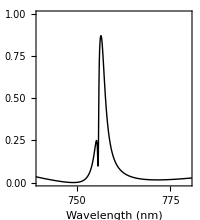

```mathematica
fit=Plot[Rp[ncav[1239800/λ],dcav,0,λ],{λ,610,850},
PlotRange->{{740,780},{0,1}},
PlotStyle->{Thin,Black},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->200,
Frame->True,
FrameStyle->Directive[Black,8,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","Reflectance"},
FrameTicksStyle->Directive[Black,6,FontFamily->"Cambria"],
AspectRatio->1.1,PlotPoints->300]
```

```mathematica
nfit[ω_,γrt_,γnrt_,λot_,γrb_,γnrb_,λob_]:={1.,nhBN[1239.8/ω],Exc[γrt,1239800/λot,γnrt,ω],nhBN[1239.8/ω],Exc[γrb,1239800/λob,γnrb,ω],nhBN[1239.8/ω],nSiO2[1239.8/ω],nSi[1239.8/ω]}
Manipulate[ 
Show[Plot[{Rp[nfit[1239800/λ,γrt,γnrt,λot,γrb,γnrb,λob],dcav,0,λ]},{λ,600,800},
PlotRange->{{710,780},{0,0.6}},
PlotStyle->{{Red,Black}},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->300,
Frame->True,
FrameStyle->Directive[Thick,Black,11,FontFamily->"Cambria"],
FrameLabel->{"Wavelength (nm)","Reflectance 0°"},
FrameTicksStyle->Directive[Black,Thick,10,FontFamily->"Cambria"],
AspectRatio->1,
PlotLegends->Placed[{"Fitting"},{Left,Bottom}],PlotPoints->300],
fit],
{{γrt,4.5},1.5,4.5},
{{γnrt,2.55},0.05,3,0.05},
{{λot,754.25},750,757,0.05},
{{γrb,4.5},1.5,4.5},
{{γnrb,0.95},0.05,3,0.05},
{{λob,753.9},750,757,0.05},
{{A,0.7},0.5,1.5},
ControlPlacement->Right]
```